```mathematica
Needs["PlotLegends`"]
```

### Average regional reading times from Grodner, Watson & Gibson

```mathematica
datasub={316.874,375.663,372.425,375.123,350.726,449.123,365.204,330.856,507.533,364.905,538.625,398.432,365.726,388.46}
```

{316.874,375.663,372.425,375.123,350.726,449.123,365.204,330.856,507.533,364.905,538.625,398.432,365.726,388.46}

```mathematica
dataobj={321.239,388.677,357.343,369.684,375.589,474.478,411.687,359.697,561.135,485.571,473.219,406.835,365.926,388.313}
```

{321.239,388.677,357.343,369.684,375.589,474.478,411.687,359.697,561.135,485.571,473.219,406.835,365.926,388.313}

```mathematica
regionalizesub={{1,2},{3,4},{5,6},{7,9},{10,11},{12,14}}
```

{{1,2},{3,4},{5,6},{7,9},{10,11},{12,14}}

```mathematica
regionalizeobj={{1,2},{3,5},{6,7},{8,9},{10,11},{12,14}}
```

{{1,2},{3,5},{6,7},{8,9},{10,11},{12,14}}

### Utilities for grouping into the regions used by Gibson

```mathematica
by[x_,y_]:=Table[{x[[i]],y[[i]]},{i,1,Length[x]}]/;Length[x]==Length[y]
```

```mathematica
modulo[l_,{start_,fin_}]:=Fold[Plus,0,Part[l,Range[start,fin]]]/(fin-start+1)
```

```mathematica
group[l_,{start_,fin_}]:= Part[l,Range[start,fin]]
```

### fit linear model linking bits to msec

```mathematica
lm=LinearModelFit[Join[by[modulo[entropyreductions[[1]],#1]&/@regionalizesub,
modulo[datasub,#1]&/@regionalizesub],
by[modulo[entropyreductions[[2]],#1]&/@regionalizeobj,
modulo[dataobj,#1]&/@regionalizeobj]],x,x]
```

```mathematica
interdigitate[a_String,b_String]:= If[a=="",b,If[b=="",a,a<>" "<>b]];
```

```mathematica
tmarkssubj=Module[{rgions=Fold[interdigitate,"",group[subjobj[[1]],#1]]&/@regionalizesub},Table[{x,rgions[[x]]},{x,1,6}]]
```

{{1,the reporter},{2,who sent},{3,the photographer},{4,to the editor},{5,hoped for},{6,a good story}}

```mathematica
tmarksobj=Module[{rgions=Fold[interdigitate,"",group[subjobj[[2]],#1]]&/@regionalizeobj},Table[{x,rgions[[x]]},{x,1,6}]]
```

{{1,the reporter},{2,who the photographer},{3,sent to},{4,the editor},{5,hoped for},{6,a good story}}

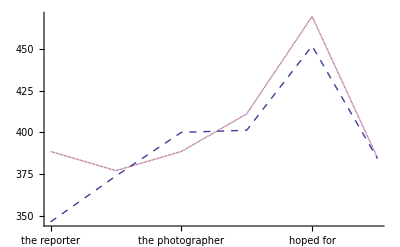

```mathematica
ListPlot[{modulo[datasub,#]&/@regionalizesub,lm/@(modulo[entropyreductions[[1]],#]&/@regionalizesub)},Joined->True,PlotStyle->{Dashed,Dashing[0]},Ticks->{tmarkssubj,Automatic}]
```

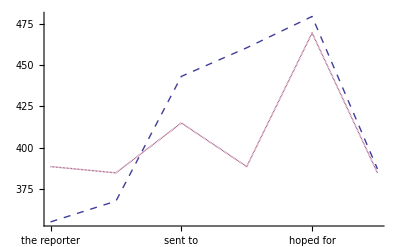

```mathematica
ListPlot[{modulo[dataobj,#]&/@regionalizeobj,lm/@(modulo[entropyreductions[[2]],#]&/@regionalizeobj)},Joined->True,PlotStyle->{Dashed,Dashing[0]},Ticks->{tmarksobj,Automatic}]
```

```mathematica
lmsurp=LinearModelFit[Join[by[modulo[surprisals[[1]],#1]&/@regionalizesub,
modulo[datasub,#1]&/@regionalizesub],
by[modulo[surprisals[[2]],#1]&/@regionalizeobj,
modulo[dataobj,#1]&/@regionalizeobj]],x,x]
```

FittedModel[474.486-29.0784 x]

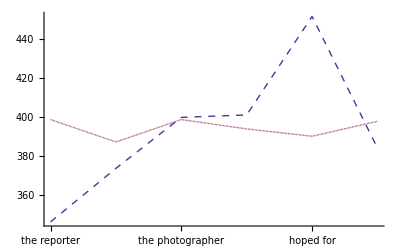

```mathematica
ListPlot[{modulo[datasub,#]&/@regionalizesub,lm/@(modulo[surprisals[[1]],#]&/@regionalizesub)},Joined->True,PlotStyle->{Dashed,Dashing[0]},Ticks->{tmarkssubj,Automatic}]
```

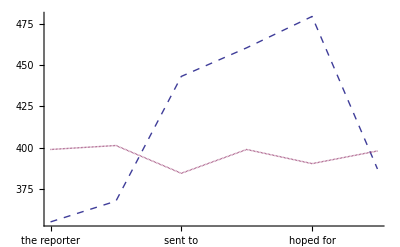

```mathematica
ListPlot[{modulo[dataobj,#]&/@regionalizeobj,lm/@(modulo[surprisals[[2]],#]&/@regionalizeobj)},Joined->True,PlotStyle->{Dashed,Dashing[0]},Ticks->{tmarksobj,Automatic}]
```

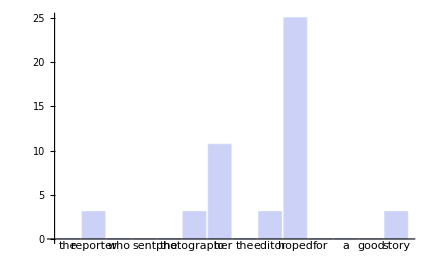
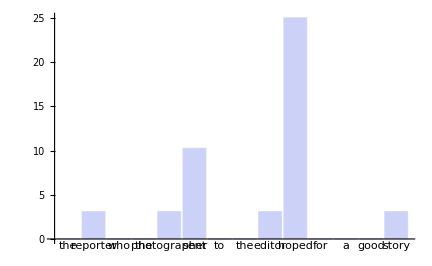

```mathematica
BarChart[entropyreductions[[#]],ChartLabels->subjobj[[#]],ImageSize->72*6]&/@ Range[1,2]
```